# 3.2

d)
SYSTEM1

NDSolve::ndsz: At t == 0.445997, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.69551, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.61683, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

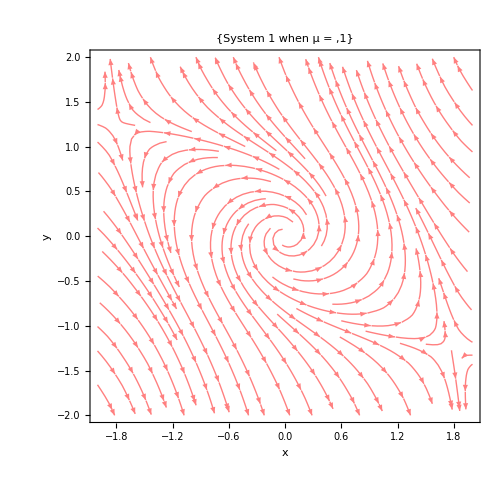

```mathematica
ClearAll["Global`*"]
(*{μ*x-3*y-1*x^3,3*x+μ*y+2*y^3}*)
(*Define systems*)
mu=1;
eq1=x'[t]==mu*x[t]-3*y[t]-1*x[t]^3;
eq2=y'[t]== 3*x[t]+mu*y[t]+2*y[t]^3;
system={eq1,eq2};

startPt={{x[0]==-2,y[0]==0.5},{x[0]==0.2,y[0]==0},{x[0]==-0.1,y[0]==0},{x[0]==2,y[0]==0},{x[0]==0,y[0]==-0.5}};

t0=0;
tMax=5;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x-3*y-1*x^3,3*x+mu*y+2*y^3},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

NDSolve::ndsz: At t == 0.829828, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.49146, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

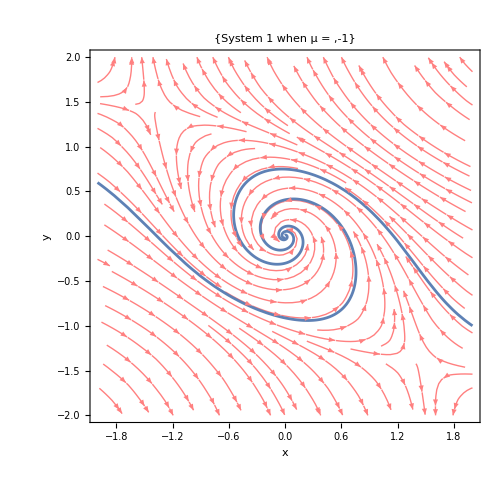

```mathematica
ClearAll["Global`*"]
(*{μ*x-3*y-1*x^3,3*x+μ*y+2*y^3}*)
(*Define systems*)
mu=-1;
eq1=x'[t]==mu*x[t]-3*y[t]-1*x[t]^3;
eq2=y'[t]== 3*x[t]+mu*y[t]+2*y[t]^3;
system={eq1,eq2};

startPt={{x[0]==-2,y[0]==0.6},{x[0]==-2,y[0]==0.3},{x[0]==-2,y[0]==-0.1},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==0.1}};

t0=0;
tMax=5;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x-3*y-1*x^3,3*x+mu*y+2*y^3},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

System 1 is subcritical when mu =0 


--------------------------------------------------------------------------------------------------

SYSTEM 2

NDSolve::ndsz: At t == 2.45302, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.24611, step size is effectively zero; singularity or stiff system suspected.

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

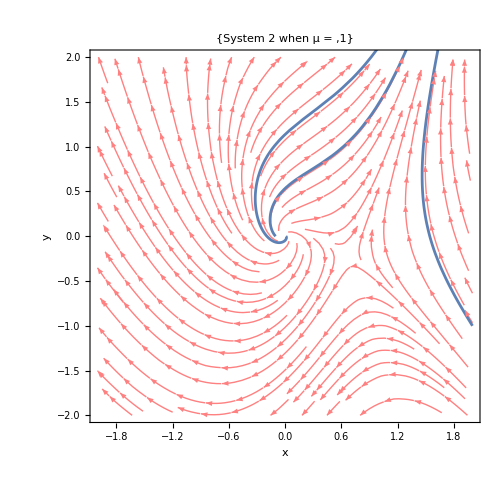

```mathematica
ClearAll["Global`*"]
(*{μ*x+y-x^2,       -x+μ*y+2*x^2}*)
(*Define systems*)
mu=1;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};

startPt={{x[0]==0,y[0]==0},{x[0]==0.01,y[0]==0},{x[0]==-0.1,y[0]==0},{x[0]==2,y[0]==-1},{x[0]==0.2,y[0]==-0.2},{x[0]==2,y[0]==-1.8}};

t0=0;
tMax=5;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 2 when μ = ",mu}]
```

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

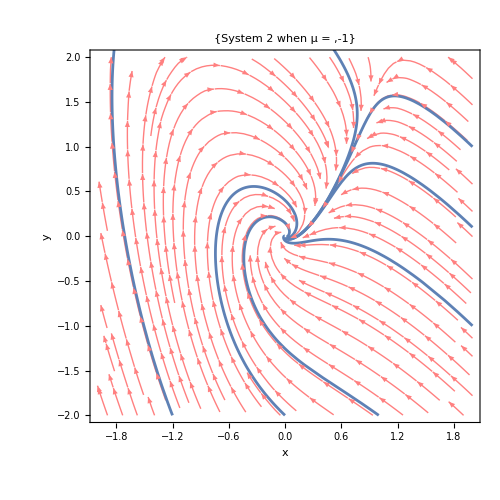

```mathematica
ClearAll["Global`*"]
(*{μ*x+y-x^2,       -x+μ*y+2*x^2}*)
(*Define systems*)
mu=-1;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};

startPt={{x[0]==1,y[0]==-2},{x[0]==0,y[0]==-2},{x[0]==-1.2,y[0]==-2},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==0.1},{x[0]==2,y[0]==1}};

t0=0;
tMax=5;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 2 when μ = ",mu}]
```

System 2 is supercritical when mu =0